# Método de los momentos dividiendo el dominio - Normal estándar

```mathematica
(*Muestra de la distribución Normal(0,1)*)
```

```mathematica
SeedRandom[1234]
```

```mathematica
data1 = RandomVariate[NormalDistribution[0,1],10001]
```

{-0.508336,-0.0706019,-1.5939,1.53659,2.67802,-1.31683,-1.09456,0.142948,0.104166,-1.67311,0.0357514,0.170186,0.934682,-0.826864,9973,0.622688,-0.538344,1.10496,-0.342243,1.0691,-0.852105,0.249137,1.09009,0.0543596,-1.12438,-1.15048,0.35102,0.954185,-0.387142}
 |  |  |  |

```mathematica
data=Delete[data1,7615]
```

{-0.508336,-0.0706019,-1.5939,1.53659,2.67802,-1.31683,-1.09456,0.142948,0.104166,-1.67311,0.0357514,0.170186,0.934682,-0.826864,9972,0.622688,-0.538344,1.10496,-0.342243,1.0691,-0.852105,0.249137,1.09009,0.0543596,-1.12438,-1.15048,0.35102,0.954185,-0.387142}
 |  |  |  |

### MOP DE GRADO 3

```mathematica
F3[x_] = Piecewise[{{a+b*x+c*x^2+d*x^3,-Infinity<x<0},{e+f*x+g*x^2+h*x^3,0≤x<Infinity}},0]
```

Piecewise[{{a+b x+c x^2+d x^3, -∞<x<0}, {e+f x+g x^2+h x^3, 0≤x<∞}, {0, True}}]

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*F3[x],{x,-4,4}]
```

-8/15 (15 a-40 b+120 c-384 d-15 e-40 f-120 g-384 h)

```mathematica
Integrate[x^2*F3[x],{x,-4,4}]
```

64/15 (5 a-15 b+48 c-160 d+5 e+15 f+48 g+160 h)

```mathematica
Integrate[x^3*F3[x],{x,-4,4}]
```

-64/105 (105 a-336 b+1120 c-3840 d-105 e-336 f-1120 g-3840 h)

```mathematica
Integrate[x^4*F3[x],{x,-4,4}]
```

1024/105 (21 a-70 b+240 c-840 d+21 e+70 f+240 g+840 h)

```mathematica
Integrate[x^5*F3[x],{x,-4,4}]
```

-2048/63 (21 a-72 b+252 c-896 d-21 e-72 f-252 g-896 h)

```mathematica
Integrate[x^6*F3[x],{x,-4,4}]
```

8192/315 (90 a-315 b+1120 c-4032 d+90 e+315 f+1120 g+4032 h)

```mathematica
Integrate[x^7*F3[x],{x,-4,4}]
```

-8192/495 (495 a-1760 b+6336 c-23040 d-495 e-1760 f-6336 g-23040 h)

```mathematica
Integrate[x^8*F3[x],{x,-4,4}]
```

262144/495 (55 a-198 b+720 c-2640 d+55 e+198 f+720 g+2640 h)

```mathematica
(*Función de las diferencias al cuadrado entre los momentos poblacionales y muestrales*)
```

```mathematica
F31[a_,b_,c_,d_,e_,f_,g_,h_]=(-8/15 (15 a-40 b+120 c-384 d-15 e-40 f-120 g-384 h)-(Apply[Plus,data])/10^4)^2+(64/15 (5 a-15 b+48 c-160 d+5 e+15 f+48 g+160 h)-(Apply[Plus,data^2])/10^4)^2+(-64/105 (105 a-336 b+1120 c-3840 d-105 e-336 f-1120 g-3840 h)-(Apply[Plus,data^3])/10^4)^2+(1024/105 (21 a-70 b+240 c-840 d+21 e+70 f+240 g+840 h)-(Apply[Plus,data^4])/10^4)^2+(-2048/63 (21 a-72 b+252 c-896 d-21 e-72 f-252 g-896 h)-(Apply[Plus,data^5])/10^4)^2+(8192/315 (90 a-315 b+1120 c-4032 d+90 e+315 f+1120 g+4032 h)-(Apply[Plus,data^6])/10^4)^2+(-8192/495 (495 a-1760 b+6336 c-23040 d-495 e-1760 f-6336 g-23040 h)-(Apply[Plus,data^7])/10^4)^2+(262144/495 (55 a-198 b+720 c-2640 d+55 e+198 f+720 g+2640 h)-(Apply[Plus,data^8])/10^4)^2
```

(2.60393-8192/495 (495 a-1760 b+6336 c-23040 d-495 e-1760 f-6336 g-23040 h))^2+(0.0566338-64/105 (105 a-336 b+1120 c-3840 d-105 e-336 f-1120 g-3840 h))^2+(0.355927-2048/63 (21 a-72 b+252 c-896 d-21 e-72 f-252 g-896 h))^2+(0.0196627-8/15 (15 a-40 b+120 c-384 d-15 e-40 f-120 g-384 h))^2+(-0.992368+64/15 (5 a-15 b+48 c-160 d+5 e+15 f+48 g+160 h))^2+(-2.9755+1024/105 (21 a-70 b+240 c-840 d+21 e+70 f+240 g+840 h))^2+(-100.868+262144/495 (55 a-198 b+720 c-2640 d+55 e+198 f+720 g+2640 h))^2+(-14.7766+8192/315 (90 a-315 b+1120 c-4032 d+90 e+315 f+1120 g+4032 h))^2

```mathematica
F3[-4]
```

a-4 b+16 c-64 d

```mathematica
F3[4]
```

e+4 f+16 g+64 h

```mathematica
Minimize[{F31[a,b,c,d,e,f,g,h],{a-4 b+16 c-64 d>0,e+4 f+16 g+64 h>0}},{a,b,c,d,e,f,g,h}]
```

{0.0000203393,{a→0.608955,b→0.500205,c→0.137263,d→0.0125678,e→0.595551,f→-0.491932,g→0.13534,h→-0.0123898}}

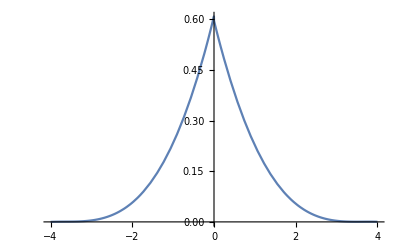

```mathematica
Plot[F3[x]/.{a->0.6089545391347432,b->0.5002052130729798,c->0.13726290825966145,d->0.012567815921834471,e->0.5955506587224156,f->-0.49193186910051623,g->0.13533995260687084,h->-0.01238984985174974},{x,-4,4}]
```

```mathematica
F32[x_]=F3[x]/.{a->0.6089545391347432,b->0.5002052130729798,c->0.13726290825966145,d->0.012567815921834471,e->0.5955506587224156,f->-0.49193186910051623,g->0.13533995260687084,h->-0.01238984985174974}
```

Piecewise[{{0.608955+0.500205 x+0.137263 x^2+0.0125678 x^3, -∞≤x<0}, {0.595551-0.491932 x+0.13534 x^2-0.0123898 x^3, 0≤x≤∞}, {0, True}}]

```mathematica
Solve[F32[x]==0,Reals]
```

{{x→-4.},{x→4.06451}}

```mathematica
(*Como no hay parte negativa, dejamos de añadir restricciones*)
```

```mathematica
(*Obtención de la densidad y representación*)
```

```mathematica
Integrate[F32[x],{x,-4,4}]
```

1.09916

```mathematica
f3[x_]=Piecewise[{{(0.6089545391347432+0.5002052130729798 x+0.13726290825966145 x^2+0.012567815921834471 x^3)/1.0991612230173007,-Infinity≤x<0},{(0.5955506587224156-0.49193186910051623 x+0.13533995260687084 x^2-0.01238984985174974 x^3)/1.0991612230173007,0≤x≤Infinity}},0]
```

Piecewise[{{0.909785 (0.608955+0.500205 x+0.137263 x^2+0.0125678 x^3), -∞≤x<0}, {0.909785 (0.595551-0.491932 x+0.13534 x^2-0.0123898 x^3), 0≤x≤∞}, {0, True}}]

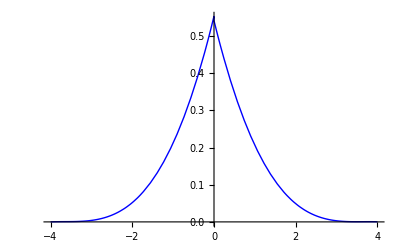

```mathematica
Plot[f3[x],{x,-4,4},PlotStyle->{Blue,Thin}]
```

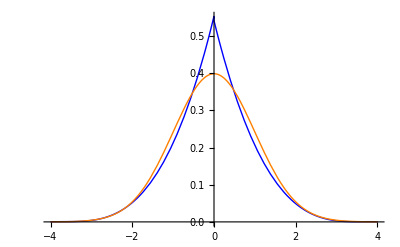

```mathematica
Plot[{f3[x],PDF[NormalDistribution[0,1],x]},{x,-4,4},PlotStyle->{{Blue,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
N[Integrate[PDF[NormalDistribution[0,1],x],{x,-4,4}]]
```

0.999937

```mathematica
F[x_]=(PDF[NormalDistribution[0,1],x])/0.9999366575163338
```

0.398968 ⅇ^(-x^2/2)

```mathematica
KL3 = N[Integrate[F[x]*Log[F[x]/f3[x]],{x,-4,4}]]
```

0.0106555

```mathematica
(*Verosimilitud*)
```

```mathematica
x3=Log[Table[f3[Extract[data,i]],{i,1,10000}]]
```

{-1.04001,-0.649118,-2.30633,-2.26388,-4.62135,-1.92969,9988,-0.658058,-1.69304,-1.72407,-0.917774,-1.52745,-0.926617}
 |  |  |  |

```mathematica
V3=Apply[Plus,x3]
```

-14242.8

### MOP DE GRADO 4

```mathematica
F4[x_] = Piecewise[{{a+b*x+c*x^2+d*x^3+e*x^4,-Infinity<x<0},{f+g*x+h*x^2+i*x^3+j*x^4,0≤x<Infinity}},0]
```

Piecewise[{{a+b x+c x^2+d x^3+e x^4, -∞<x<0}, {f+g x+h x^2+i x^3+j x^4, 0≤x<∞}, {0, True}}]

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*F4[x],{x,-4,4}]
```

-8/15 (15 a-40 b+120 c-384 d+1280 e-15 f-40 g-120 h-384 i-1280 j)

```mathematica
Integrate[x^2*F4[x],{x,-4,4}]
```

64/105 (35 a-105 b+336 c-1120 d+3840 e+35 f+105 g+336 h+1120 i+3840 j)

```mathematica
Integrate[x^3*F4[x],{x,-4,4}]
```

-64/105 (105 a-336 b+1120 c-3840 d+13440 e-105 f-336 g-1120 h-3840 i-13440 j)

```mathematica
Integrate[x^4*F4[x],{x,-4,4}]
```

1024/315 (63 a-210 b+720 c-2520 d+8960 e+63 f+210 g+720 h+2520 i+8960 j)

```mathematica
Integrate[x^5*F4[x],{x,-4,4}]
```

-2048/315 (105 a-360 b+1260 c-4480 d+16128 e-105 f-360 g-1260 h-4480 i-16128 j)

```mathematica
Integrate[x^6*F4[x],{x,-4,4}]
```

1/3465 8192 (990 a-3465 b+12320 c-44352 d+161280 e+990 f+3465 g+12320 h+44352 i+161280 j)

```mathematica
Integrate[x^7*F4[x],{x,-4,4}]
```

-8192/495 (495 a-1760 b+6336 c-23040 d+84480 e-495 f-1760 g-6336 h-23040 i-84480 j)

```mathematica
Integrate[x^8*F4[x],{x,-4,4}]
```

1/6435 262144 (715 a-2574 b+9360 c-34320 d+126720 e+715 f+2574 g+9360 h+34320 i+126720 j)

```mathematica
Integrate[x^9*F4[x],{x,-4,4}]
```

-1/15015 524288 (3003 a-10920 b+40040 c-147840 d+549120 e-3003 f-10920 g-40040 h-147840 i-549120 j)

```mathematica
Integrate[x^10*F4[x],{x,-4,4}]
```

1/15015 4194304 (1365 a-5005 b+18480 c-68640 d+256256 e+1365 f+5005 g+18480 h+68640 i+256256 j)

```mathematica
(*Función de las diferencias al cuadrado entre los momentos poblacionales y muestrales*)
```

```mathematica
F41[a_,b_,c_,d_,e_,f_,g_,h_,i_,j_]=(-8/15 (15 a-40 b+120 c-384 d+1280 e-15 f-40 g-120 h-384 i-1280 j)-(Apply[Plus,data])/10^4)^2+(64/105 (35 a-105 b+336 c-1120 d+3840 e+35 f+105 g+336 h+1120 i+3840 j)-(Apply[Plus,data^2])/10^4)^2+(-64/105 (105 a-336 b+1120 c-3840 d+13440 e-105 f-336 g-1120 h-3840 i-13440 j)-(Apply[Plus,data^3])/10^4)^2+(1024/315 (63 a-210 b+720 c-2520 d+8960 e+63 f+210 g+720 h+2520 i+8960 j)-(Apply[Plus,data^4])/10^4)^2+(-2048/315 (105 a-360 b+1260 c-4480 d+16128 e-105 f-360 g-1260 h-4480 i-16128 j)-(Apply[Plus,data^5])/10^4)^2+(1/3465 8192 (990 a-3465 b+12320 c-44352 d+161280 e+990 f+3465 g+12320 h+44352 i+161280 j)-(Apply[Plus,data^6])/10^4)^2+(-8192/495 (495 a-1760 b+6336 c-23040 d+84480 e-495 f-1760 g-6336 h-23040 i-84480 j)-(Apply[Plus,data^7])/10^4)^2+(1/6435 262144 (715 a-2574 b+9360 c-34320 d+126720 e+715 f+2574 g+9360 h+34320 i+126720 j)-(Apply[Plus,data^8])/10^4)^2+(-1/15015 524288 (3003 a-10920 b+40040 c-147840 d+549120 e-3003 f-10920 g-40040 h-147840 i-549120 j)-(Apply[Plus,data^9])/10^4)^2+(1/15015 4194304 (1365 a-5005 b+18480 c-68640 d+256256 e+1365 f+5005 g+18480 h+68640 i+256256 j)-(Apply[Plus,data^10])/10^4)^2
```

(17.1996-(524288 (3003 a-10920 b+40040 c-147840 d+549120 e-3003 f-10920 g-40040 h-147840 i-549120 j))/15015)^2+(2.60393-8192/495 (495 a-1760 b+6336 c-23040 d+84480 e-495 f-1760 g-6336 h-23040 i-84480 j))^2+(0.355927-2048/315 (105 a-360 b+1260 c-4480 d+16128 e-105 f-360 g-1260 h-4480 i-16128 j))^2+(0.0566338-64/105 (105 a-336 b+1120 c-3840 d+13440 e-105 f-336 g-1120 h-3840 i-13440 j))^2+(0.0196627-8/15 (15 a-40 b+120 c-384 d+1280 e-15 f-40 g-120 h-384 i-1280 j))^2+(-0.992368+64/105 (35 a-105 b+336 c-1120 d+3840 e+35 f+105 g+336 h+1120 i+3840 j))^2+(-2.9755+1024/315 (63 a-210 b+720 c-2520 d+8960 e+63 f+210 g+720 h+2520 i+8960 j))^2+(-100.868+(262144 (715 a-2574 b+9360 c-34320 d+126720 e+715 f+2574 g+9360 h+34320 i+126720 j))/6435)^2+(-14.7766+(8192 (990 a-3465 b+12320 c-44352 d+161280 e+990 f+3465 g+12320 h+44352 i+161280 j))/3465)^2+(-860.688+(4194304 (1365 a-5005 b+18480 c-68640 d+256256 e+1365 f+5005 g+18480 h+68640 i+256256 j))/15015)^2

```mathematica
(*Minimización de F41 sujeta a restricciones*)
```

```mathematica
Minimize[{F41[a,b,c,d,e,f,g,h,i,j],{a-4 b+16 c-64 d+256 e>0,f+4 g+16 h+64 i+256 j>0}},{a,b,c,d,e,f,g,h,i,j}]
```

{54.1008,{a→86.8637,b→160.334,c→101.198,d→26.5735,e→2.48883,f→44.6136,g→-72.0665,h→41.0844,i→-9.94181,j→0.870067}}

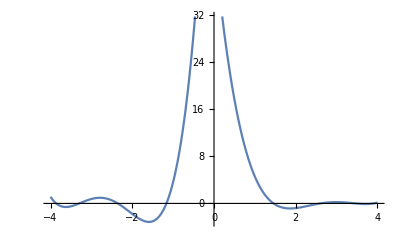

```mathematica
Plot[F4[x]/.{a->86.86369945190236,b->160.33430403106118,c->101.1980586001049,d->26.57354353612119,e->2.4888258337545333,f->44.6136457089953,g->-72.06646396941062,h->41.08438331540055,i->-9.941808028885713,j->0.8700674364731915},{x,-4,4}]
```

```mathematica
F42[x_]=F4[x]/.{a->86.86369945190236,b->160.33430403106118,c->101.1980586001049,d->26.57354353612119,e->2.4888258337545333,f->44.6136457089953,g->-72.06646396941062,h->41.08438331540055,i->-9.941808028885713,j->0.8700674364731915}
```

Piecewise[{{86.8637+160.334 x+101.198 x^2+26.5735 x^3+2.48883 x^4, -∞<x<0}, {44.6136-72.0665 x+41.0844 x^2-9.94181 x^3+0.870067 x^4, 0≤x<∞}, {0, True}}]

```mathematica
Solve[F42[x]==0,Reals]
```

{{x→-3.86199},{x→-3.29611},{x→-2.35463},{x→-1.16442},{x→1.45695},{x→2.60534},{x→3.45987},{x→3.90432}}

```mathematica
APN = -Integrate[F42[x],{x,-3.8619871410254767,-3.296105440317194}]-Integrate[F42[x],{x,-2.3546285207817883,-1.1644195702839069}]-Integrate[F42[x],{x,1.456954140815304,2.605337646384239}]-Integrate[F42[x],{x,3.459865200123146,3.904322860244897}]
```

3.16524

```mathematica
AT = Integrate[F42[x],{x,-4,-3.8619871410254767}]-Integrate[F42[x],{x,-3.8619871410254767,-3.296105440317194}]+Integrate[F42[x],{x,-3.296105440317194,-2.3546285207817883}]-Integrate[F42[x],{x,-2.3546285207817883,-1.1644195702839069}]+Integrate[F42[x],{x,-1.1644195702839069,1.456954140815304}]-Integrate[F42[x],{x,1.456954140815304,2.605337646384239}]+Integrate[F42[x],{x,2.605337646384239,3.459865200123146}]-Integrate[F42[x],{x,3.459865200123146,3.904322860244897}]+Integrate[F42[x],{x,3.904322860244897,4}]
```

59.3113

```mathematica
APN/AT
```

0.0533666

```mathematica
(*Como el área de la parte negativa es superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
F4[(-3.8619871410254767-3.296105440317194)/2]
```

a-3.57905 b+12.8096 c-45.8461 d+164.085 e

```mathematica
F4[(-2.3546285207817883-1.1644195702839069)/2]
```

a-1.75952 b+3.09592 c-5.44735 d+9.58475 e

```mathematica
F4[(1.456954140815304+2.605337646384239)/2]
```

f+2.03115 g+4.12555 h+8.3796 i+17.0202 j

```mathematica
F4[(3.459865200123146+3.904322860244897)/2]
```

f+3.68209 g+13.5578 h+49.9212 i+183.814 j

```mathematica
Minimize[{F41[a,b,c,d,e,f,g,h,i,j],{a-4 b+16 c-64 d+256 e>0,f+4 g+16 h+64 i+256 j>0,
a-3.5790462906713354 b+12.809572350768246 c-45.84605240710319 d+164.08514380956632 e>0,
a-1.7595240455328476 b+3.095924866808278 c-5.447354246312244 d+9.584750780921855 e>0,
f+2.0311458935997715 g+4.1255536410872145 h+8.379601336919881 i+17.020192845487973 j>0,
f+3.6820940301840217 g+13.557816447116812 h+49.92115500225955 i+183.81438681371114 j>0}},{a,b,c,d,e,f,g,h,i,j}]
```

{3.12379×10^6,{a→5356.95,b→7719.05,c→4003.85,d→893.569,e→72.8369,f→2255.36,g→-2950.41,h→1409.88,i→-293.166,j→22.4647}}

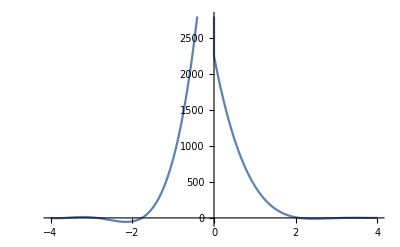

```mathematica
Plot[F4[x]/.{a->5356.953454717503,b->7719.046364953451,c->4003.8495825728396,d->893.5689615410133,e->72.83693062706274,f->2255.36312583447,g->-2950.412324630982,h->1409.8771454862233,i->-293.1656273606532,j->22.464736422170528},{x,-4,4}]
```

```mathematica
F43[x_]=F4[x]/.{a->5356.953454717503,b->7719.046364953451,c->4003.8495825728396,d->893.5689615410133,e->72.83693062706274,f->2255.36312583447,g->-2950.412324630982,h->1409.8771454862233,i->-293.1656273606532,j->22.464736422170528}
```

Piecewise[{{5356.95+7719.05 x+4003.85 x^2+893.569 x^3+72.8369 x^4, -∞<x<0}, {2255.36-2950.41 x+1409.88 x^2-293.166 x^3+22.4647 x^4, 0≤x<∞}, {0, True}}]

```mathematica
Solve[F43[x]==0,Reals]
```

{{x→-3.99693},{x→-3.64427},{x→-2.86363},{x→-1.76324},{x→2.08639},{x→3.1721},{x→3.80931},{x→3.98224}}

```mathematica
APN1 = - Integrate[F43[x],{x,-3.9969325402708917,-3.6442689810311206}]-Integrate[F43[x],{x,-2.8636332791391648,-1.7632406641364793}]-Integrate[F43[x],{x,2.0863851886777818,3.17209593451614}]-Integrate[F43[x],{x,3.809314952139484,3.982240295061175}]
```

46.2286

```mathematica
AT1 = Integrate[F43[x],{x,-4,-3.9969325402708917}]- Integrate[F43[x],{x,-3.9969325402708917,-3.6442689810311206}]+Integrate[F43[x],{x,-3.6442689810311206,-2.8636332791391648}]-Integrate[F43[x],{x,-2.8636332791391648,-1.7632406641364793}]+Integrate[F43[x],{x,-1.7632406641364793,2.0863851886777818}]-Integrate[F43[x],{x,2.0863851886777818,3.17209593451614}]+Integrate[F43[x],{x,3.17209593451614,3.809314952139484}]-Integrate[F43[x],{x,3.809314952139484,3.982240295061175}]+Integrate[F43[x],{x,3.982240295061175,4}]
```

4245.66

```mathematica
APN1/AT1
```

0.0108884

```mathematica
(*Como el área de la parte negativa sigue siendo superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
F4[(-3.9969325402708917-3.6442689810311206)/2]
```

a-3.8206 b+14.597 c-55.7693 d+213.072 e

```mathematica
F4[(-2.8636332791391648-1.7632406641364793)/2]
```

a-2.31344 b+5.35199 c-12.3815 d+28.6438 e

```mathematica
F4[(2.0863851886777818+3.17209593451614)/2]
```

f+2.62924 g+6.91291 h+18.1757 i+47.7883 j

```mathematica
F4[(3.809314952139484+3.982240295061175)/2]
```

f+3.89578 g+15.1771 h+59.1265 i+230.344 j

```mathematica
Minimize[{F41[a,b,c,d,e,f,g,h,i,j],{a-4 b+16 c-64 d+256 e>0,f+4 g+16 h+64 i+256 j>0,
a-3.5790462906713354 b+12.809572350768246 c-45.84605240710319 d+164.08514380956632 e>0,
a-1.7595240455328476 b+3.095924866808278 c-5.447354246312244 d+9.584750780921855 e>0,
f+2.0311458935997715 g+4.1255536410872145 h+8.379601336919881 i+17.020192845487973 j>0,
f+3.6820940301840217 g+13.557816447116812 h+49.92115500225955 i+183.81438681371114 j>0,
a-3.820600760651006 b+14.596990172287045 c-55.769271755455144 d+213.07212208984458 e>0,
a-2.313436971637822 b+5.351990621740777 c-12.381492976194007 d+28.64380361520123 e>0,
f+2.629240561596961 g+6.912905930746704 h+18.175692671623427 i+47.78826840735295 j>0,
f+3.8957776236003294 g+15.17708329254503 h+59.12654148261534 i+230.3438572688495 j>0}},{a,b,c,d,e,f,g,h,i,j}]
```

{5.96426×10^6,{a→1228.3,b→1353.54,c→544.068,d→94.6312,e→6.00555,f→-2461.54,g→3619.59,h→-1899.21,i→426.585,j→-34.8845}}

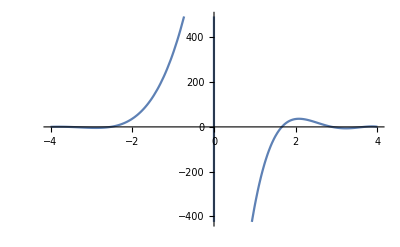

```mathematica
Plot[F4[x]/.{a->1228.300336708536,b->1353.5394692195764,c->544.0679001564408,d->94.63117887617543,e->6.005553669486085,f->-2461.5432603068666,g->3619.5895742474318,h->-1899.2140399381835,i->426.5849999856777,j->-34.88452842083942},{x,-4,4}]
```

```mathematica
(*Como el área de la parte negativa es superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
F44[x_]=F4[x]/.{a->1228.300336708536,b->1353.5394692195764,c->544.0679001564408,d->94.63117887617543,e->6.005553669486085,f->-2461.5432603068666,g->3619.5895742474318,h->-1899.2140399381835,i->426.5849999856777,j->-34.88452842083942}
```

Piecewise[{{1228.3+1353.54 x+544.068 x^2+94.6312 x^3+6.00555 x^4, -∞<x<0}, {-2461.54+3619.59 x-1899.21 x^2+426.585 x^3-34.8845 x^4, 0≤x<∞}, {0, True}}]

```mathematica
Solve[F44[x]==0,Reals]
```

{{x→-5.63634},{x→-4.0395},{x→-3.55342},{x→-2.52802},{x→1.66031},{x→2.88759},{x→3.66762},{x→4.01296}}

```mathematica
F4[(-3.5534240544236386-2.528016820739499)/2]
```

a-3.04072 b+9.24598 c-28.1144 d+85.4882 e

```mathematica
F4[1.6603089556158097/2]
```

f+0.830154 g+0.689156 h+0.572106 i+0.474937 j

```mathematica
F4[(2.8875923619364205+3.667624947603306)/2]
```

f+3.27761 g+10.7427 h+35.2104 i+115.406 j

```mathematica
Minimize[{F41[a,b,c,d,e,f,g,h,i,j],{a-4 b+16 c-64 d+256 e>0,f+4 g+16 h+64 i+256 j>0,
a-3.5790462906713354 b+12.809572350768246 c-45.84605240710319 d+164.08514380956632 e>0,
a-1.7595240455328476 b+3.095924866808278 c-5.447354246312244 d+9.584750780921855 e>0,
f+2.0311458935997715 g+4.1255536410872145 h+8.379601336919881 i+17.020192845487973 j>0,
f+3.6820940301840217 g+13.557816447116812 h+49.92115500225955 i+183.81438681371114 j>0,
a-3.820600760651006 b+14.596990172287045 c-55.769271755455144 d+213.07212208984458 e>0,
a-2.313436971637822 b+5.351990621740777 c-12.381492976194007 d+28.64380361520123 e>0,
f+2.629240561596961 g+6.912905930746704 h+18.175692671623427 i+47.78826840735295 j>0,
f+3.8957776236003294 g+15.17708329254503 h+59.12654148261534 i+230.3438572688495 j>0,
a-3.0407204375815686 b+9.245980779526246 c-28.114442721791818 d+85.48816057536877 e>0,
f+0.8301544778079049 g+0.6891564570245152 h+0.5721063187091323 i+0.4749366222585825 j>0,
f+3.277608654769863 g+10.742718493822311 h+35.210427111108274 i+115.40600063751191 j>0}},{a,b,c,d,e,f,g,h,i,j}]
```

{254278.,{a→4.46124,b→5.20914,c→2.27505,d→0.440338,e→0.0318651,f→6.3047,g→-7.50484,h→3.32355,i→-0.649305,j→0.0472503}}

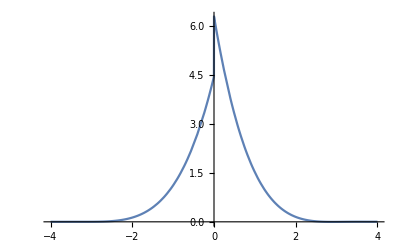

```mathematica
Plot[F4[x]/.{a->4.461242853594442,b->5.209136968538976,c->2.275047989790258,d->0.4403380570228985,e->0.03186513736971056,f->6.304699725969827,g->-7.504836165260885,h->3.3235468379998223,i->-0.6493048915075006,j->0.04725025409815506},{x,-4,4}]
```

```mathematica
F45[x_]=F4[x]/.{a->4.461242853594442,b->5.209136968538976,c->2.275047989790258,d->0.4403380570228985,e->0.03186513736971056,f->6.304699725969827,g->-7.504836165260885,h->3.3235468379998223,i->-0.6493048915075006,j->0.04725025409815506}
```

Piecewise[{{4.46124+5.20914 x+2.27505 x^2+0.440338 x^3+0.0318651 x^4, -∞<x<0}, {6.3047-7.50484 x+3.32355 x^2-0.649305 x^3+0.0472503 x^4, 0≤x<∞}, {0, True}}]

```mathematica
Solve[F45[x]==0,Reals]
```

{{x→2.73268},{x→3.16273}}

```mathematica
APN2=-Integrate[F45[x],{x,2.7326750857278843,3.1627311382342316}]
```

0.000631346

```mathematica
AT2 = Integrate[F45[x],{x,-4,2.7326750857278843}]-Integrate[F45[x],{x,2.7326750857278843,3.1627311382342316}]+Integrate[F45[x],{x,3.1627311382342316,4}]
```

7.25562

```mathematica
APN2/AT2
```

0.0000870148

```mathematica
(*Como el área de la parte negativa es inferior al 1% del área total, dejamos de añadir restricciones*)
```

```mathematica
(*Obtención de la densidad y representación*)
```

```mathematica
FindMinimum[F45[x],{x,2.9}]
```

{-0.00227454,{x→2.90588}}

```mathematica
F46[x_]=Piecewise[{{4.461242853594442+5.209136968538976 x+2.275047989790258 x^2+0.4403380570228985 x^3+0.03186513736971056 x^4,-Infinity≤x<0},{6.304699725969827-7.504836165260885 x+3.3235468379998223 x^2-0.6493048915075006 x^3+0.04725025409815506 x^4+0.0022745389301395136,0≤x≤Infinity}},0]
```

Piecewise[{{4.46124+5.20914 x+2.27505 x^2+0.440338 x^3+0.0318651 x^4, -∞≤x<0}, {6.30697-7.50484 x+3.32355 x^2-0.649305 x^3+0.0472503 x^4, 0≤x≤∞}, {0, True}}]

```mathematica
Integrate[F46[x],{x,-4,4}]
```

7.26346

```mathematica
f4[x_]=Piecewise[{{(4.461242853594442+5.209136968538976 x+2.275047989790258 x^2+0.4403380570228985 x^3+0.03186513736971056 x^4)/7.263456529773784,-Infinity<x<0},{(6.304699725969827-7.504836165260885 x+3.3235468379998223 x^2-0.6493048915075006 x^3+0.04725025409815506 x^4+0.0022745389301395136)/7.263456529773784,0≤x<Infinity}},0]
```

Piecewise[{{0.137675 (4.46124+5.20914 x+2.27505 x^2+0.440338 x^3+0.0318651 x^4), -∞<x<0}, {0.137675 (6.30697-7.50484 x+3.32355 x^2-0.649305 x^3+0.0472503 x^4), 0≤x<∞}, {0, True}}]

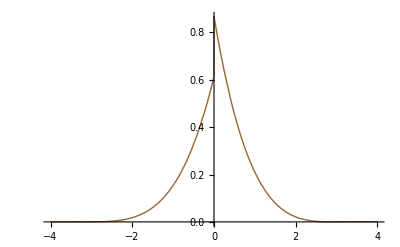

```mathematica
Plot[f4[x],{x,-4,4},PlotStyle->{Brown,Thin}]
```

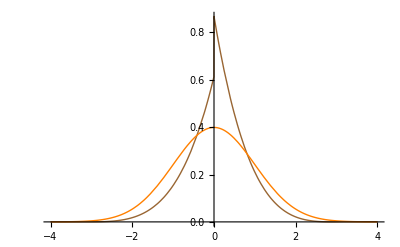

```mathematica
Plot[{f4[x],PDF[NormalDistribution[0,1],x]},{x,-4,4},PlotStyle->{{Brown,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
KL4 = N[Integrate[F[x]*Log[F[x]/f4[x]],{x,-4,4}]]
```

0.127639

```mathematica
(*Verosimilitud*)
```

```mathematica
x4=Log[Table[f4[Extract[data,i]],{i,1,10000}]]
```

{-1.13039,-0.570734,-3.00231,-2.61761,-7.43798,-2.43376,-2.0305,-0.315109,-0.267157,-3.18125,-0.183974,-0.349144,-1.4512,-1.59392,9972,-0.962995,-1.17181,-1.74642,-0.908634,-1.68231,-1.63308,-0.449506,-1.7197,-0.206425,-2.08226,-2.12812,-0.582961,-1.48388,-0.967367}
 |  |  |  |

```mathematica
V4=Apply[Plus,x4]
```

-15402.6

### MOP DE GRADO 5

```mathematica
F5[x_] = Piecewise[{{a+b*x+c*x^2+d*x^3+e*x^4+f*x^5,-Infinity<x<0},{g+h*x+i*x^2+j*x^3+k*x^4+l*x^5,0≤x<Infinity}},0]
```

Piecewise[{{a+b x+c x^2+d x^3+e x^4+f x^5, -∞<x<0}, {g+h x+i x^2+j x^3+k x^4+l x^5, 0≤x<∞}, {0, True}}]

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*F5[x],{x,-4,4}]
```

-8/105 (105 a-280 b+840 c-2688 d+8960 e-30720 f-105 g-280 h-840 i-2688 j-8960 k-30720 l)

```mathematica
Integrate[x^2*F5[x],{x,-4,4}]
```

64/105 (35 a-105 b+336 c-1120 d+3840 e-13440 f+35 g+105 h+336 i+1120 j+3840 k+13440 l)

```mathematica
Integrate[x^3*F5[x],{x,-4,4}]
```

-64/315 (315 a-1008 b+3360 c-11520 d+40320 e-143360 f-315 g-1008 h-3360 i-11520 j-40320 k-143360 l)

```mathematica
Integrate[x^4*F5[x],{x,-4,4}]
```

1024/315 (63 a-210 b+720 c-2520 d+8960 e-32256 f+63 g+210 h+720 i+2520 j+8960 k+32256 l)

```mathematica
Integrate[x^5*F5[x],{x,-4,4}]
```

-1/3465 2048 (1155 a-3960 b+13860 c-49280 d+177408 e-645120 f-1155 g-3960 h-13860 i-49280 j-177408 k-645120 l)

```mathematica
Integrate[x^6*F5[x],{x,-4,4}]
```

1/3465 8192 (990 a-3465 b+12320 c-44352 d+161280 e-591360 f+990 g+3465 h+12320 i+44352 j+161280 k+591360 l)

```mathematica
Integrate[x^7*F5[x],{x,-4,4}]
```

-1/6435 8192 (6435 a-22880 b+82368 c-299520 d+1098240 e-4055040 f-6435 g-22880 h-82368 i-299520 j-1098240 k-4055040 l)

```mathematica
Integrate[x^8*F5[x],{x,-4,4}]
```

1/45045 262144 (5005 a-18018 b+65520 c-240240 d+887040 e-3294720 f+5005 g+18018 h+65520 i+240240 j+887040 k+3294720 l)

```mathematica
Integrate[x^9*F5[x],{x,-4,4}]
```

-1/15015 524288 (3003 a-10920 b+40040 c-147840 d+549120 e-2050048 f-3003 g-10920 h-40040 i-147840 j-549120 k-2050048 l)

```mathematica
Integrate[x^10*F5[x],{x,-4,4}]
```

1/15015 4194304 (1365 a-5005 b+18480 c-68640 d+256256 e-960960 f+1365 g+5005 h+18480 i+68640 j+256256 k+960960 l)

```mathematica
Integrate[x^11*F5[x],{x,-4,4}]
```

-1/23205 4194304 (7735 a-28560 b+106080 c-396032 d+1485120 e-5591040 f-7735 g-28560 h-106080 i-396032 j-1485120 k-5591040 l)

```mathematica
Integrate[x^12*F5[x],{x,-4,4}]
```

1/69615 67108864 (5355 a-19890 b+74256 c-278460 d+1048320 e-3960320 f+5355 g+19890 h+74256 i+278460 j+1048320 k+3960320 l)

```mathematica
F51[a_,b_,c_,d_,e_,f_,g_,h_,i_,j_,k_,l_]=(-8/105 (105 a-280 b+840 c-2688 d+8960 e-30720 f-105 g-280 h-840 i-2688 j-8960 k-30720 l)-(Apply[Plus,data])/10^4)^2+(64/105 (35 a-105 b+336 c-1120 d+3840 e-13440 f+35 g+105 h+336 i+1120 j+3840 k+13440 l)-(Apply[Plus,data^2])/10^4)^2+(-64/315 (315 a-1008 b+3360 c-11520 d+40320 e-143360 f-315 g-1008 h-3360 i-11520 j-40320 k-143360 l)-(Apply[Plus,data^3])/10^4)^2+(1024/315 (63 a-210 b+720 c-2520 d+8960 e-32256 f+63 g+210 h+720 i+2520 j+8960 k+32256 l)-(Apply[Plus,data^4])/10^4)^2+(-1/3465 2048 (1155 a-3960 b+13860 c-49280 d+177408 e-645120 f-1155 g-3960 h-13860 i-49280 j-177408 k-645120 l)-(Apply[Plus,data^5])/10^4)^2+(1/3465 8192 (990 a-3465 b+12320 c-44352 d+161280 e-591360 f+990 g+3465 h+12320 i+44352 j+161280 k+591360 l)-(Apply[Plus,data^6])/10^4)^2+(-1/6435 8192 (6435 a-22880 b+82368 c-299520 d+1098240 e-4055040 f-6435 g-22880 h-82368 i-299520 j-1098240 k-4055040 l)-(Apply[Plus,data^7])/10^4)^2+(1/45045 262144 (5005 a-18018 b+65520 c-240240 d+887040 e-3294720 f+5005 g+18018 h+65520 i+240240 j+887040 k+3294720 l)-(Apply[Plus,data^8])/10^4)^2+(-1/15015 524288 (3003 a-10920 b+40040 c-147840 d+549120 e-2050048 f-3003 g-10920 h-40040 i-147840 j-549120 k-2050048 l)-(Apply[Plus,data^9])/10^4)^2+(1/15015 4194304 (1365 a-5005 b+18480 c-68640 d+256256 e-960960 f+1365 g+5005 h+18480 i+68640 j+256256 k+960960 l)-(Apply[Plus,data^10])/10^4)^2+(-1/23205 4194304 (7735 a-28560 b+106080 c-396032 d+1485120 e-5591040 f-7735 g-28560 h-106080 i-396032 j-1485120 k-5591040 l)-(Apply[Plus,data^11])/10^4)^2+(1/69615 67108864 (5355 a-19890 b+74256 c-278460 d+1048320 e-3960320 f+5355 g+19890 h+74256 i+278460 j+1048320 k+3960320 l)-(Apply[Plus,data^12])/10^4)^2
```

(67.3493-(4194304 (7735 a-28560 b+106080 c-396032 d+1485120 e-5591040 f-7735 g-28560 h-106080 i-396032 j-1485120 k-5591040 l))/23205)^2+(2.60393-(8192 (6435 a-22880 b+82368 c-299520 d+1098240 e-4055040 f-6435 g-22880 h-82368 i-299520 j-1098240 k-4055040 l))/6435)^2+(17.1996-(524288 (3003 a-10920 b+40040 c-147840 d+549120 e-2050048 f-3003 g-10920 h-40040 i-147840 j-549120 k-2050048 l))/15015)^2+(0.355927-(2048 (1155 a-3960 b+13860 c-49280 d+177408 e-645120 f-1155 g-3960 h-13860 i-49280 j-177408 k-645120 l))/3465)^2+(0.0566338-64/315 (315 a-1008 b+3360 c-11520 d+40320 e-143360 f-315 g-1008 h-3360 i-11520 j-40320 k-143360 l))^2+(0.0196627-8/105 (105 a-280 b+840 c-2688 d+8960 e-30720 f-105 g-280 h-840 i-2688 j-8960 k-30720 l))^2+(-0.992368+64/105 (35 a-105 b+336 c-1120 d+3840 e-13440 f+35 g+105 h+336 i+1120 j+3840 k+13440 l))^2+(-2.9755+1024/315 (63 a-210 b+720 c-2520 d+8960 e-32256 f+63 g+210 h+720 i+2520 j+8960 k+32256 l))^2+(-14.7766+(8192 (990 a-3465 b+12320 c-44352 d+161280 e-591360 f+990 g+3465 h+12320 i+44352 j+161280 k+591360 l))/3465)^2+(-860.688+(4194304 (1365 a-5005 b+18480 c-68640 d+256256 e-960960 f+1365 g+5005 h+18480 i+68640 j+256256 k+960960 l))/15015)^2+(-100.868+(262144 (5005 a-18018 b+65520 c-240240 d+887040 e-3294720 f+5005 g+18018 h+65520 i+240240 j+887040 k+3294720 l))/45045)^2+(-8625.74+(67108864 (5355 a-19890 b+74256 c-278460 d+1048320 e-3960320 f+5355 g+19890 h+74256 i+278460 j+1048320 k+3960320 l))/69615)^2

```mathematica
F5[4]
```

g+4 h+16 i+64 j+256 k+1024 l

```mathematica
Minimize[{F51[a,b,c,d,e,f,g,h,i,j,k,l],{a-4 b+16 c-64 d+256 e-1024 f>0,g+4 h+16 i+64 j+256 k+1024 l>0}},{a,b,c,d,e,f,g,h,i,j,k,l}]
```

{171.087,{a→34.8977,b→46.459,c→20.0153,d→2.32572,e→-0.391454,f→-0.0780053,g→48.0812,h→-62.1894,i→23.4333,j→-0.369559,k→-1.31018,l→0.180745}}

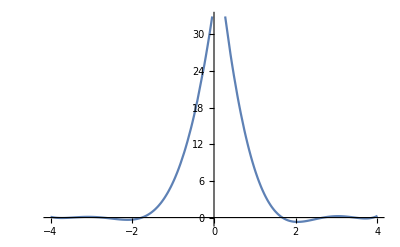

```mathematica
Plot[F5[x]/.{a->34.89771355141857,b->46.45903636860304,c->20.015343863057144,d->2.325717774249091,e->-0.3914542780591964,f->-0.07800531084238448,g->48.081154035469396,h->-62.18935433044647,i->23.433340677471058,j->-0.36955946164621456,k->-1.310183599862378,l->0.18074549793669334},{x,-4,4}]
```

```mathematica
F51[x_]=F5[x]/.{a->34.89771355141857,b->46.45903636860304,c->20.015343863057144,d->2.325717774249091,e->-0.3914542780591964,f->-0.07800531084238448,g->48.081154035469396,h->-62.18935433044647,i->23.433340677471058,j->-0.36955946164621456,k->-1.310183599862378,l->0.18074549793669334}
```

Piecewise[{{34.8977+46.459 x+20.0153 x^2+2.32572 x^3-0.391454 x^4-0.0780053 x^5, -∞<x<0}, {48.0812-62.1894 x+23.4333 x^2-0.369559 x^3-1.31018 x^4+0.180745 x^5, 0≤x<∞}, {0, True}}]

```mathematica
Solve[F51[x]==0,Reals]
```

{{x→-3.89929},{x→-3.47953},{x→-2.72687},{x→-1.76473},{x→1.67324},{x→2.67332},{x→3.44521},{x→3.89208}}

```mathematica
APN=-Integrate[F51[x],{x,-3.899288591442936,-3.479525433826304}]-Integrate[F51[x],{x,-2.726871248162293,-1.764730095328984}]-Integrate[F51[x],{x,1.673239099013276,2.6733172497346533}]-Integrate[F51[x],{x,3.445211932668012,3.892082248230731}]
```

0.721456

```mathematica
AT=Integrate[F51[x],{x,-4,-3.899288591442936}]-Integrate[F51[x],{x,-3.899288591442936,-3.479525433826304}]+Integrate[F51[x],{x,-3.479525433826304,-2.726871248162293}]-Integrate[F51[x],{x,-2.726871248162293,-1.764730095328984}]+Integrate[F51[x],{x,-1.764730095328984,1.673239099013276}]-Integrate[F51[x],{x,1.673239099013276,2.6733172497346533}]+Integrate[F51[x],{x,2.6733172497346533,3.445211932668012}]-Integrate[F51[x],{x,3.445211932668012,3.892082248230731}]+Integrate[F51[x],{x,3.892082248230731,4}]
```

46.7239

```mathematica
APN/AT
```

0.0154408

```mathematica
(*Como el área de la parte negativa es superior al 1% del área total, seguimos añadiendo restricciones*)
```

```mathematica
F5[(-3.899288591442936-3.479525433826304)/2]
```

a-3.68941 b+13.6117 c-50.2192 d+185.279 e-683.57 f

```mathematica
F5[(-2.726871248162293-1.764730095328984)/2]
```

a-2.2458 b+5.04362 c-11.327 d+25.4381 e-57.1289 f

```mathematica
F5[(1.673239099013276+2.6733172497346533)/2]
```

g+2.17328 h+4.72314 i+10.2647 j+22.308 k+48.4816 l

```mathematica
F5[(3.445211932668012+3.892082248230731)/2]
```

g+3.66865 h+13.459 i+49.3762 j+181.144 k+664.553 l

```mathematica
Minimize[{F51[a,b,c,d,e,f,g,h,i,j,k,l],{a-4 b+16 c-64 d+256 e-1024 f>0,g+4 h+16 i+64 j+256 k+1024 l>0,
a-3.6894070126346197 b+13.611724104877508 c-50.21919036658277 d+185.2790331073034 e-683.569764040247 f>0,
a-2.2458006717456387 b+5.043620657213162 c-11.3269666599995 d+25.438109333867327 e-57.12892302993824 f>0,
g+2.173278174373965 h+4.723138023210233 i+10.264692780398594 j+22.30803278629427 k+48.481560767672164 l>0,
g+3.6686470904493715 h+13.45897147426264 i+49.37621653949472 j+181.14391314501546 k+664.5530899120746 l>0}},{a,b,c,d,e,f,g,h,i,j,k,l}]
```

{4.74766×10^11,{a→0.416057,b→-0.201266,c→0.709369,d→0.198782,e→-0.0649604,f→-0.0163906,g→0.442566,h→0.262265,i→0.630577,j→-0.0951588,k→-0.108629,l→0.0217957}}

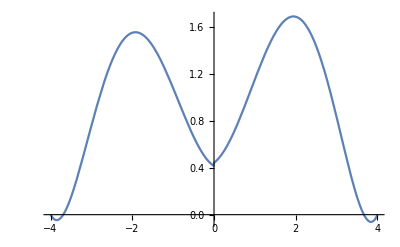

```mathematica
Plot[F5[x]/.{a->0.41605657251778416,b->-0.20126626598134145,c->0.7093686820727805,d->0.1987815022541976,e->-0.064960405538578,f->-0.016390593855540463,g->0.44256633905205095,h->0.26226521962686844,i->0.6305768815568942,j->-0.09515875494120522,k->-0.10862901605246243,l->0.021795734308431763},{x,-4,4}]
```

```mathematica
F52[x_]=F5[x]/.{a->0.41605657251778416,b->-0.20126626598134145,c->0.7093686820727805,d->0.1987815022541976,e->-0.064960405538578,f->-0.016390593855540463,g->0.44256633905205095,h->0.26226521962686844,i->0.6305768815568942,j->-0.09515875494120522,k->-0.10862901605246243,l->0.021795734308431763}
```

Piecewise[{{0.416057-0.201266 x+0.709369 x^2+0.198782 x^3-0.0649604 x^4-0.0163906 x^5, -∞<x<0}, {0.442566+0.262265 x+0.630577 x^2-0.0951588 x^3-0.108629 x^4+0.0217957 x^5, 0≤x<∞}, {0, True}}]

```mathematica
Solve[F52[x]==0,Reals]
```

{{x→-3.99538},{x→-3.68942},{x→3.66865},{x→3.99939}}

```mathematica
APN1 = -Integrate[F52[x],{x,-3.995380295804291,-3.689421059508878}]-Integrate[F52[x],{x,3.668646158584053,3.999394366306479}]
```

0.0229614

```mathematica
AT1 = Integrate[F52[x],{x,-4,-3.995380295804291}]-Integrate[F52[x],{x,-3.995380295804291,-3.689421059508878}]+Integrate[F52[x],{x,-3.689421059508878,3.668646158584053}]-Integrate[F52[x],{x,3.668646158584053,3.999394366306479}]+Integrate[F52[x],{x,3.999394366306479,4}]
```

7.47941

```mathematica
APN1/AT1
```

0.00306994

```mathematica
(*Como el área de la parte negativa ya es inferior al 1% del área total, dejamos de añadir restricciones*)
```

```mathematica
FindMinimum[F52[x],{x,-3.5}]
```

{-0.046152,{x→-3.84965}}

```mathematica
FindMinimum[F52[x],{x,3.5}]
```

{-0.0616383,{x→3.84276}}

```mathematica
F53[x_]= Piecewise[{{0.41605657251778416-0.20126626598134145 x+0.7093686820727805 x^2+0.1987815022541976 x^3-0.064960405538578 x^4-0.016390593855540463 x^5+0.04615202423430276,-Infinity<x<0},{0.44256633905205095+0.26226521962686844 x+0.6305768815568942 x^2-0.09515875494120522 x^3-0.10862901605246243 x^4+0.021795734308431763 x^5+0.061638325834930896,0≤x<Infinity}},0]
```

Piecewise[{{0.462209-0.201266 x+0.709369 x^2+0.198782 x^3-0.0649604 x^4-0.0163906 x^5, -∞<x<0}, {0.504205+0.262265 x+0.630577 x^2-0.0951588 x^3-0.108629 x^4+0.0217957 x^5, 0≤x<∞}, {0, True}}]

```mathematica
Integrate[F53[x],{x,-4,4}]
```

7.86465

```mathematica
f5[x_]=Piecewise[{{(0.41605657251778416-0.20126626598134145 x+0.7093686820727805 x^2+0.1987815022541976 x^3-0.064960405538578 x^4-0.016390593855540463 x^5+0.04615202423430276)/7.8646536464425285,-Infinity<x<0},{(0.44256633905205095+0.26226521962686844 x+0.6305768815568942 x^2-0.09515875494120522 x^3-0.10862901605246243 x^4+0.021795734308431763 x^5+0.061638325834930896)/7.8646536464425285,0≤x<Infinity}},0]
```

Piecewise[{{0.127151 (0.462209-0.201266 x+0.709369 x^2+0.198782 x^3-0.0649604 x^4-0.0163906 x^5), -∞<x<0}, {0.127151 (0.504205+0.262265 x+0.630577 x^2-0.0951588 x^3-0.108629 x^4+0.0217957 x^5), 0≤x<∞}, {0, True}}]

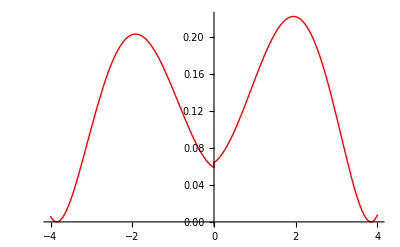

```mathematica
Plot[f5[x],{x,-4,4},PlotStyle->{Red,Thin}]
```

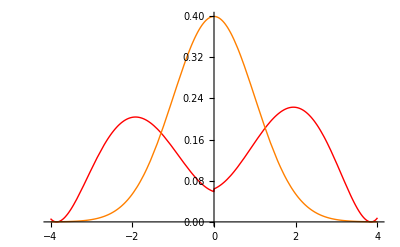

```mathematica
Plot[{f5[x],PDF[NormalDistribution[0,1],x]},{x,-4,4},PlotStyle->{{Red,Thin},{Orange,Thin}}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
N[Integrate[PDF[NormalDistribution[0,1],x],{x,-4,4}]]
```

0.999937

```mathematica
KL5 = N[Integrate[F[x]*Log[F[x]/f5[x]],{x,-4,4}]]
```

0.759937

```mathematica
(*Verosimilitud*)
```

```mathematica
x5=Log[Table[f5[Extract[data,i]],{i,1,10000}]]
```

{-2.39376,-2.79659,-1.63738,-1.57261,-1.78763,-1.74539,-1.87655,-2.6525,-2.68182,-1.61799,-2.72717,-2.63058,-1.91813,-2.08542,9972,-2.1962,-2.36292,-1.79274,-2.56425,-1.81742,-2.06348,-2.56191,-1.80286,-2.71571,-1.85668,-1.83987,-2.46538,-1.90273,-2.51872}
 |  |  |  |

```mathematica
V5=Apply[Plus,x5]
```

-21822.7

### EVOLUCIÓN

```mathematica
(*Representación gráfica de todas juntas*)
```

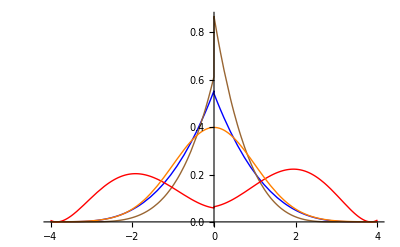

```mathematica
Plot[{f3[x],f4[x],f5[x],PDF[NormalDistribution[0,1],x]},{x,-4,4},PlotStyle->{{Blue,Thin},{Brown,Thin},{Red,Thin},{Orange,Thin}},PlotRange->Full]
```

### GRÁFICO DIVERGENCIAS

```mathematica
DKL={{{3,0.010655525130234784}},{{4,0.12763895235162234}},{{5,0.7599371011177195}}}
```

{{{3,0.0106555}},{{4,0.127639}},{{5,0.759937}}}

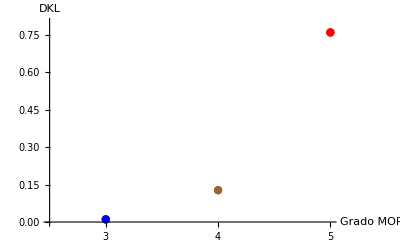

```mathematica
g1 =ListPlot[DKL,PlotStyle->{{Blue,Thin,PointSize[0.015]},{Brown,Thin,PointSize[0.015]},{Red,Thin,PointSize[0.015]}},AxesLabel->{"Grado MOP","DKL"},AxesOrigin->{2.5,0},AxesStyle->Directive[Black, 12],PlotRange->{0,0.8},Ticks->{{3,4,5}, Automatic}]
```

```mathematica
DKL1 ={{3,0.010655525130234784},{4,0.12763895235162234},{5,0.7599371011177195}}
```

{{3,0.0106555},{4,0.127639},{5,0.759937}}

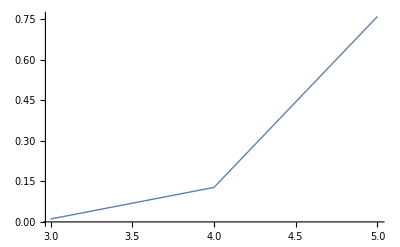

```mathematica
g2 = ListLinePlot[DKL1,PlotStyle->Thin,PlotRange->Full]
```

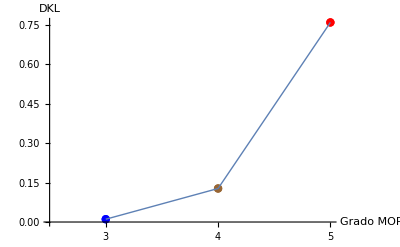

```mathematica
GDivergenciasNormalMADividiendo=Show[g1,g2]
```

```mathematica
(*Comparación gráfico divergencias momentos y momentos aproximados*)
```

```mathematica
(*Gráfico Divergencias KL método de los momentos aproximado*)
```

```mathematica
GDivergenciasNormalMADividiendo
```

-Graphics-

```mathematica
(*Gráfico Divergencias KL método de los momentos*)
```

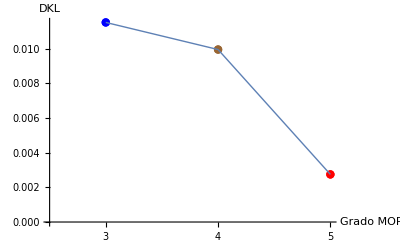

```mathematica
GDivergenciasNormalMDividiendo
```

### GRÁFICO VEROSIMILITUDES

```mathematica
V = {{{3,-14242.839948316787}},{{4,-15402.636784025599}},{{5,-21822.708281350173}}}
```

{{{3,-14242.8}},{{4,-15402.6}},{{5,-21822.7}}}

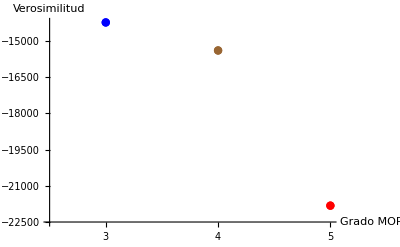

```mathematica
h1=ListPlot[V,PlotStyle->{{Blue,Thin,PointSize[0.015]},{Brown,Thin,PointSize[0.015]},{Red,Thin,PointSize[0.015]}},AxesLabel->{"Grado MOP","Verosimilitud"},AxesOrigin->{2.5,-22500},AxesStyle->Directive[Black, 12],PlotRange->Full,Ticks->{{3,4,5}, Automatic}]
```

### MOMENTOS

```mathematica
(*Muestrales*)
```

```mathematica
Table[(Apply[Plus,data^i])/10000,{i,1,12}]
```

{-0.0196627,0.992368,-0.0566338,2.9755,-0.355927,14.7766,-2.60393,100.868,-17.1996,860.688,-67.3493,8625.74}

```mathematica
(*Con los modelos estimados*)
```

```mathematica
f3estimada = Table[Integrate[x^i*f3[x],{x,-4,4}],{i,1,12}]
```

{-0.0157891,0.901266,-0.0542804,2.70845,-0.323196,13.4433,-2.36905,91.7678,-18.7929,790.424,-147.866,8073.25}

```mathematica
f3estimada = Table[Integrate[x^i*f4[x],{x,-4,4}],{i,1,12}]
```

{0.0827925,0.541369,0.0930552,1.08544,0.374496,4.29412,3.72291,29.7947,49.0757,304.399,684.642,3770.06}

```mathematica
f3estimada = Table[Integrate[x^i*f5[x],{x,-4,4}],{i,1,12}]
```

{0.0834818,3.8863,0.4617,24.2359,3.33224,186.242,27.9237,1626.7,259.623,15538.2,2617.46,158855.}

```mathematica
Table[{Integrate[x^i*f3[x],{x,-4,4}],Integrate[x^i*f4[x],{x,-4,4}],Integrate[x^i*f5[x],{x,-4,4}]},{i,1,12}]
```

{{-0.0157891,0.0827925,0.0834818},{0.901266,0.541369,3.8863},{-0.0542804,0.0930552,0.4617},{2.70845,1.08544,24.2359},{-0.323196,0.374496,3.33224},{13.4433,4.29412,186.242},{-2.36905,3.72291,27.9237},{91.7678,29.7947,1626.7},{-18.7929,49.0757,259.623},{790.424,304.399,15538.2},{-147.866,684.642,2617.46},{8073.25,3770.06,158855.}}